```mathematica
file1=<<"/Users/ruppell/Math/temp/lambdaNtest_clean.txt";
```

```mathematica
pos1[name_]:=Select[name,(Abs@#[[2,-4]]<1*^4)&];
pos2[name_]:=Select[name,(Abs@#[[2,-5]]<1*^4)&];
pos3[name_]:=Select[name,(Abs@#[[2,-3]]<1*^4)&];
pos4[name_]:=Select[name,(Abs@#[[2,-2]]<1*^4)&];
pos5[name_]:=Select[name,(Abs@#[[2,-1]]<1*^4)&];
posH[name_]:=Select[name,(Abs@#[[3,6,1]]<2*^-4)&];
posS[name_]:=Select[name,(Abs@#[[2,10]]<1*^4)&];
posB[name_]:=Select[name,(#[[9,1]]≠-1)&];
```

```mathematica
file1=(pos1@pos2@pos3@pos4@pos5@posH@posS@posB@file1);
```

```mathematica
Dimensions@file1
```

{1000,10}

```mathematica
snuLSP[name_]:=Select[name,#[[3,5,1]]<Abs@#[[3,1,1]]&];
χ0LSP[name_]:=Select[name,#[[3,5,1]]>Abs@#[[3,1,1]]&];
snuLeft[name_]:=Select[name,#[[4,10,1,4]]^2+#[[4,10,1,8]]^2<0.99&];
snuRight[name_]:=Select[name,#[[4,10,1,4]]^2+#[[4,10,1,8]]^2>0.99&];
bsg[name_]:=Select[name,(#[[9,1]]<4.97*^-4&&#[[9,1]]>2.13*^-4)&];
ΔMd[name_]:=Select[name,(#[[9,2]]<5.15*^-1&&#[[9,2]]>4.99*^-1)&];
ΔMs[name_]:=Select[name,(#[[9,3]]<1.753*^1&&#[[9,3]]>1.801*^1)&];
bsμμ[name_]:=Select[name,(#[[9,4]]<1.1*^-8)&];
bτν[name_]:=Select[name,(#[[9,5]]<2.45*^-4&&#[[9,5]]>8.9*^-5)&];
dϵ[name_]:=Select[name,(#[[10,2,1]]<1.43*^-27&&#[[10,2,1]]>-0.5*^-28)&];
dμ[name_]:=Select[name,(#[[10,2,2]]<0.8*^-19)&];
BRτμγ[name_]:=Select[name,(#[[10,3,1]]<4.4*^-8)&];
BRτϵγ[name_]:=Select[name,(#[[10,3,2]]<3.3*^-8)&];
BRμϵγ[name_]:=Select[name,(#[[10,3,3]]<1.2*^-11)&];
h1[name_]:=Select[name,(#[[3,6,2]]<128&&#[[3,6,2]]>123)&];
h23[name_]:=Select[name,((#[[3,6,3]]<128&&#[[3,6,3]]>123)||(#[[3,6,4]]<128&&#[[3,6,4]]>123))&];
h123[name_]:=Select[name,((#[[3,6,2]]<128&&#[[3,6,2]]>123)||(#[[3,6,3]]<128&&#[[3,6,3]]>123)||(#[[3,6,4]]<128&&#[[3,6,4]]>123))&];
dm[name_]:=Select[name,(#[[6,1]]<0.1311&&#[[6,1]]>0.0941)&];
dmup[limU_,limD_][name_]:=Select[name,(#[[6,1]]<limU&&#[[6,1]]>limD)&];
```

```mathematica
cuts=BRμϵγ@BRτϵγ@BRτμγ@dμ@dϵ@bτν@bsμμ@bsg@#&;
```

```mathematica
pName={"M1","M2","M3","M0","Mtau","MQ","MNR","tanβ","v","vevS","Atop","Abtm","Atau","An11","An12","An13","AlambdaN","Yn11","Yn12","Yn13","lambda","lambdaN","kappa","PhisPI","Phi2PI","ksi","Alambda","Akappa","mh1","mh2","mS"};
```

```mathematica
ListPointPlot3D[
Transpose@{(snuLSP@cuts@file1)[[;;,3,5,1]],Log[10,(snuLSP@cuts@file1)[[;;,2,22]]],Log[10,(snuLSP@cuts@file1)[[;;,6,1]]]},
BoxRatios->{1,1,1}]
```

-Graphics3D-

```mathematica
{{"Spectrum","gHZZ","RD","Channels","DM -- Nucleon", "bsgamma et al", "edm et al"}}~Join~(snuLSP@dm@cuts@file1)[[;;,{3,5,6,7,8,9,10}]]//TableForm
```

Spectrum | gHZZ | RD | Channels | DM -- Nucleon | bsgamma et al | edm et al
224.932 | -254.691 | 315.567 | 613.767 | 2000.6 |  |  | 
242.315 | 613.718 |  |  |  |  |  | 
0 | 2434.87 |  |  |  |  |  | 
-2.947×10^-12 | 0 | -3.93493×10^-9 | 22.8296 |  |  |  | 
204.453 | 332.403 | 354.271 | 354.271 | 354.271 | 354.271 | 354.271 | 354.271
0.0000305176 | 126.002 | 207.271 | 2073.75 | 2433.71 | 2435.58 |  | 
356.681 | 362.619 | 362.619 | 363.043 | 363.043 | 368.886 |  | 
998.584 | 999.369 |  |  |  |  |  | 
1000.32 | 1001.73 |  |  |  |  |  | 
814.746 | 1179.84 |  |  |  |  |  | 
999.301 | 1002.76 |  |  |  |  |  |  | 0.478327 |  | 
0.425102 |  | 
0.0748915 |  | 
3.01392×10^-6 |  | 
0.0214555 |  | 
0.0002207 |  | 
0.001623 | 0.00921281 | 2.54709×10^-6 | 0.116209
~n1
26.6307 | 6.26×10^-9 | ~n1 ~n1 | s S
0.000011 | ~n1 ~n1 | b B
0.0000204 | ~n1 ~n1 | c C
2.33×10^-9 | ~n1 ~n1 | e2 E2
6.59×10^-7 | ~n1 ~n1 | e3 E3
0.418 | ~n1 ~n1 | h1 h1
0 | ~n1 ~n1 | h2 h2
0.00202 | ~n1 ~n1 | n4 n4
0.00202 | ~n1 ~n1 | N4 N4
0.267 | ~n1 ~n1 | W+ W-
0.125 | ~n1 ~n1 | Z Z
0.658 | ~o1 ~o1 | b B
14.1 | ~o1 ~o1 | h1 h1
1.35 | ~o1 ~o1 | h2 h2
9180. | ~o1 ~o1 | W+ W-
1390. | ~o1 ~o1 | Z Z | -5.76972×10^-10 | -5.76972×10^-10 | 0 | 0
-5.81857×10^-10 | -5.81857×10^-10 | 0 | 0
1.44193×10^-10 | 1.44193×10^-10 | 0 | 0
1.46645×10^-10 | 1.46645×10^-10 | 0 | 0 | 0.000363365
0.596824
20.6778
3.54154×10^-9
0.000131559
7.84703×10^-10 | 1.92669×10^-15 | 8.2374×10^-11 | 4.01622×10^-8
1.15113×10^-27 | 2.38021×10^-25 | -1.91549×10^-22
5.12029×10^-20 | 8.85872×10^-20 | 1.33259×10^-18
224.932 | -254.691 | 315.567 | 613.767 | 2000.6 |  |  | 
242.315 | 613.718 |  |  |  |  |  | 
0 | 2434.87 |  |  |  |  |  | 
2.572×10^-12 | 0 | -2.24792×10^-9 | 39.962 |  |  |  | 
130.776 | 354.271 | 354.271 | 354.271 | 354.271 | 354.271 | 354.271 | 370.596
0.0000305176 | 126.002 | 207.271 | 2073.75 | 2433.71 | 2435.58 |  | 
356.681 | 362.619 | 362.619 | 363.043 | 363.043 | 368.886 |  | 
998.584 | 999.369 |  |  |  |  |  | 
1000.32 | 1001.73 |  |  |  |  |  | 
814.746 | 1179.84 |  |  |  |  |  | 
999.301 | 1002.76 |  |  |  |  |  |  | 0.478327 |  | 
0.425102 |  | 
0.0748915 |  | 
3.01392×10^-6 |  | 
0.0214555 |  | 
0.0002207 |  | 
0.001623 | 0.00921281 | 2.54709×10^-6 | 0.121399
~n1
23.7284 | 0.0000196 | ~n1 ~n1 | s S
0.0344 | ~n1 ~n1 | b B
0.00743 | ~n1 ~n1 | c C
7.31×10^-6 | ~n1 ~n1 | e2 E2
0.00206 | ~n1 ~n1 | e3 E3
8.65 | ~n1 ~n1 | h1 h1
0 | ~n1 ~n1 | h2 h2
0.251 | ~n1 ~n1 | n4 n4
0.251 | ~n1 ~n1 | N4 N4
29.2 | ~n1 ~n1 | W+ W-
12.5 | ~n1 ~n1 | Z Z
0.658 | ~o1 ~o1 | b B
14.1 | ~o1 ~o1 | h1 h1
1.35 | ~o1 ~o1 | h2 h2
9180. | ~o1 ~o1 | W+ W-
1390. | ~o1 ~o1 | Z Z | -1.57982×10^-9 | -1.57982×10^-9 | 0 | 0
-1.59319×10^-9 | -1.59319×10^-9 | 0 | 0
1.07551×10^-9 | 1.07551×10^-9 | 0 | 0
1.09379×10^-9 | 1.09379×10^-9 | 0 | 0 | 0.000363365
0.596824
20.6778
3.54154×10^-9
0.000131559
7.84703×10^-10 | 1.92669×10^-15 | 8.2374×10^-11 | 4.01622×10^-8
1.15113×10^-27 | 2.38021×10^-25 | -1.91549×10^-22
2.50702×10^-21 | 1.01762×10^-20 | 7.99872×10^-21
224.932 | -254.691 | 315.567 | 613.767 | 2000.6 |  |  | 
242.315 | 613.718 |  |  |  |  |  | 
0 | 2434.87 |  |  |  |  |  | 
2.572×10^-12 | 0 | -3.9269×10^-9 | 22.8762 |  |  |  | 
204.287 | 332.511 | 354.271 | 354.271 | 354.271 | 354.271 | 354.271 | 354.271
0.0000305176 | 126.002 | 207.271 | 2073.75 | 2433.71 | 2435.58 |  | 
356.681 | 362.619 | 362.619 | 363.043 | 363.043 | 368.886 |  | 
998.584 | 999.369 |  |  |  |  |  | 
1000.32 | 1001.73 |  |  |  |  |  | 
814.746 | 1179.84 |  |  |  |  |  | 
999.301 | 1002.76 |  |  |  |  |  |  | 0.478327 |  | 
0.425102 |  | 
0.0748915 |  | 
3.01392×10^-6 |  | 
0.0214555 |  | 
0.0002207 |  | 
0.001623 | 0.00921281 | 2.54709×10^-6 | 0.119804
~n1
25.2557 | 6.31×10^-9 | ~n1 ~n1 | s S
0.0000111 | ~n1 ~n1 | b B
0.0000207 | ~n1 ~n1 | c C
2.35×10^-9 | ~n1 ~n1 | e2 E2
6.65×10^-7 | ~n1 ~n1 | e3 E3
0.42 | ~n1 ~n1 | h1 h1
0 | ~n1 ~n1 | h2 h2
0.00204 | ~n1 ~n1 | n4 n4
0.00204 | ~n1 ~n1 | N4 N4
0.269 | ~n1 ~n1 | W+ W-
0.126 | ~n1 ~n1 | Z Z
0.658 | ~o1 ~o1 | b B
14.1 | ~o1 ~o1 | h1 h1
1.35 | ~o1 ~o1 | h2 h2
9180. | ~o1 ~o1 | W+ W-
1390. | ~o1 ~o1 | Z Z | -5.7862×10^-10 | -5.7862×10^-10 | 0 | 0
-5.83518×10^-10 | -5.83518×10^-10 | 0 | 0
1.45017×10^-10 | 1.45017×10^-10 | 0 | 0
1.47482×10^-10 | 1.47482×10^-10 | 0 | 0 | 0.000363365
0.596824
20.6778
3.54154×10^-9
0.000131559
7.84703×10^-10 | 1.92669×10^-15 | 8.23739×10^-11 | 4.01622×10^-8
1.15113×10^-27 | 2.38021×10^-25 | -1.91549×10^-22
3.13695×10^-20 | 9.93334×10^-20 | 2.73548×10^-19

```mathematica
{pName[[{4,7,8,10,17,21,22,23,24,25,26,27,28,29,30,31}]]}~Join~(snuLSP@dm@cuts@file1)[[;;,2,{4,7,8,10,17,21,22,23,24,25,26,27,28,29,30,31}]]//TableForm
```

M0 | MNR | tanβ | vevS | AlambdaN | lambda | lambdaN | kappa | PhisPI | Phi2PI | ksi | Alambda | Akappa | mh1 | mh2 | mS
360 | 275 | 9.5 | 1250 | 610 | 0.2 | 0.00913185 | 0.8 | 0.25 | 0.03 | -675 | 1638.24 | 90.3057 | 2408.48 | 170.702 | 0.+1351.74 ⅈ
360 | 275 | 9.5 | 1250 | 610 | 0.2 | 0.0159848 | 0.8 | 0.25 | 0.03 | -675 | 1638.24 | 90.3057 | 2408.48 | 170.702 | 0.+1351.74 ⅈ
360 | 275 | 9.5 | 1250 | 610 | 0.2 | 0.00915047 | 0.8 | 0.25 | 0.03 | -675 | 1638.24 | 90.3057 | 2408.48 | 170.702 | 0.+1351.74 ⅈ

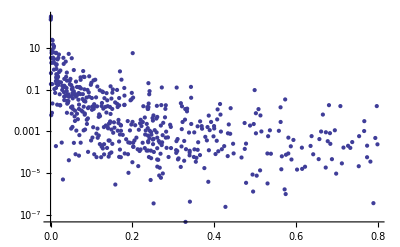

```mathematica
ListLogPlot[
Transpose@{(snuLSP@file1)[[;;,2,22]],(snuLSP@file1)[[;;,6,1]]}]
```

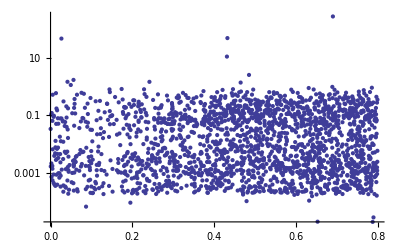

```mathematica
ListLogPlot[
Transpose@{(χ0LSP@file1)[[;;,2,22]],(χ0LSP@file1)[[;;,6,1]]}]
```